```mathematica
Clear["Global`*"]
```

1 - 8 Direction Fields, Solution Curves
Graph a direction field.  In the field graph several solution curves, particularly those passing through the given points (x,y).

1. y' = 1 + y^2, (π/4, 1)

{{y→Function[{x},Tan[x+C[1]]]}}

```mathematica
dfield=VectorPlot[{1,1+ y^2},{x,-4,4},{y,-4,4},Axes->True,VectorScale->{Automatic},AxesLabel->{"x","dydx=1+y^2"},GridLines->{{π/4},{1}}];
solu=DSolve[{y'[x]-1-y[x]^2==0, y[π/4]==1},y,x];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
ppp1=Plot[y[x]/.solu,{x,-4,4},PlotStyle->{Pink,Medium}];
pppl=ListPlot[{{π/4,1}},PlotStyle->{Red,Large},PlotMarkers->{□,19}];
```

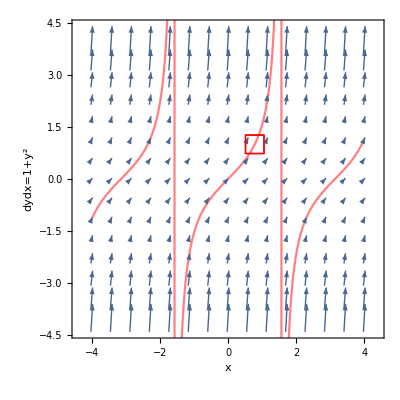

```mathematica
Show[dfield,ppp1,pppl ]
```

```mathematica
Clear["Global`*"]
```

2. y[x] y'[x] + 4x = 0, (1,1), (0,2)

```mathematica
sol1 =DSolve[{y[x] y'[x]+4x==0,y[1]==1}, y, x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y→Function[{x},√(5-4 x^2)]}}

```mathematica
pppl1=ListPlot[{{1,1}},PlotStyle->{Pink,Large},PlotMarkers->{□,19}];
```

```mathematica
sol2 =DSolve[{y[x] y'[x]+4x==0,y[0]==2}, y, x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y→Function[{x},2 √(1-x^2)]}}

```mathematica
pppl2=ListPlot[{{0,2}},PlotStyle->{Red,Large},PlotMarkers->{□,19}];
```

```mathematica
dfield1=VectorPlot[{1,-4x(1/y)},{x,-2,2},{y,-2,2},Axes->True,AxesLabel->{"x","dydx=(-4x)/y[x]"},VectorScale->{Large},VectorPoints ->{10},GridLines->{{0,1},{1,2}}];
ppp1=Plot[y[x]/.sol1,{x,-2,2},PlotStyle->{Pink,Medium}];
ppp2=Plot[y[x]/.sol2,{x,-2,2},PlotStyle->{Red,Medium}];
```

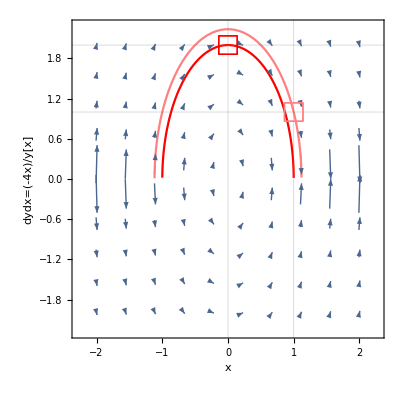

```mathematica
Show[dfield1,ppp1,ppp2,pppl1,pppl2]
```

```mathematica
Clear["Global`*"]
```

3. y' = 1 - y^2, (0,0), (2,1/2)

```mathematica
pp1 = DSolve[{y'[x]+y[x]^2==1,y[0]==0},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},(-1+ⅇ^(2 x))/(1+ⅇ^(2 x))]}}

```mathematica
pppl1=ListPlot[{{0,0}},PlotStyle->{Blue,Large},PlotMarkers->{□,19}];
```

```mathematica
pp2 = DSolve[{y'[x]+y[x]^2==1,y[2]==1/2},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},(-ⅇ^4+3 ⅇ^(2 x))/(ⅇ^4+3 ⅇ^(2 x))]}}

```mathematica
pppl2=ListPlot[{{2,1/2}},PlotStyle->{Red,Large},PlotMarkers->{□,19}];
```

```mathematica
dfield1=VectorPlot[{1,1-y^2},{x,-3,3},{y,-2,2},Axes->True,VectorScale->{Automatic},AxesLabel->{"x","dydx=1-y^2"},GridLines->{{2},{1/2}}];
ppp1=Plot[y[x]/.pp1,{x,-3,3},PlotStyle->{Blue,Medium}];
ppp2=Plot[y[x]/.pp2,{x,-3,3},PlotStyle->{Red,Medium}];
```

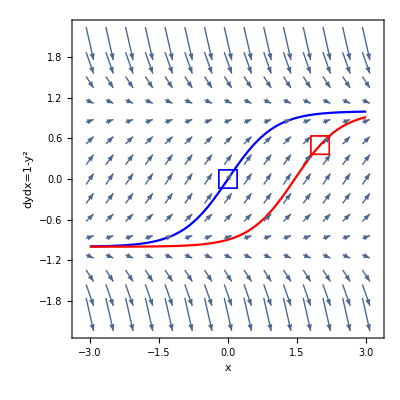

```mathematica
Show[dfield1,ppp1,ppp2,pppl1,pppl2]
```

```mathematica
Clear["Global`*"]
```

4. y' = 2y - y^2, (0,0), (0,1), (0,2), (0,3)

```mathematica
pp1 = DSolve[{y'[x]-2 y[x]+y[x]^2==0,y[0]==0},y,x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
pp2 = DSolve[{y'[x]-2 y[x]+y[x]^2==0,y[0]==1},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},(2 ⅇ^(2 x))/(1+ⅇ^(2 x))]}}

```mathematica
ppp2=Plot[y[x]/.pp2,{x,-4,4},PlotStyle->{Red,Medium}];
```

```mathematica
pppl2=ListPlot[{{0,1}},PlotStyle->{Red,Large},PlotMarkers->{□,19}];
```

```mathematica
pp3 = DSolve[{y'[x]-2 y[x]+y[x]^2==0,y[0]==2},y,x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
pp4 = DSolve[{y'[x]-2 y[x]+y[x]^2==0,y[0]==3},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},(6 ⅇ^(2 x))/(-1+3 ⅇ^(2 x))]}}

```mathematica
ppp4=Plot[y[x]/.pp4,{x,-4,4},PlotStyle->{Blue,Medium}];
```

```mathematica
pppl4=ListPlot[{{0,3}},PlotStyle->{Blue,Large},PlotMarkers->{□,19}];
```

```mathematica
dfield1=VectorPlot[{1,2y-y^2},{x,-4,4},{y,-4,4},Axes->True,VectorScale->{Automatic},AxesLabel->{"x","dydx=2y-y^2"},GridLines->{{0},{1,3}}];
```

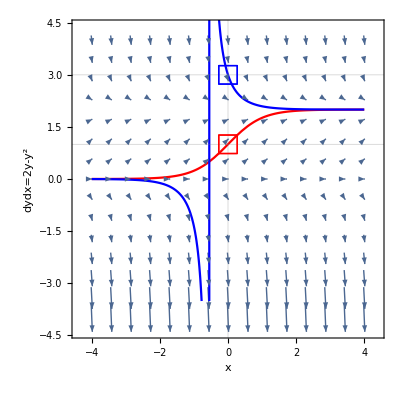

```mathematica
Show[dfield1,ppp2,ppp4,pppl2,pppl4]
```

```mathematica
Clear["Global`*"]
```

5. y' = x - 1/y, (1,1/2)

```mathematica
pp1=NDSolve[{y'[x]==x-1/y[x],y[1]==1/2},y,{x,-4,1.2}]
```

{{y→InterpolatingFunction[{{-4., 1.2}}, <>]}}

```mathematica
pp1x=NDSolve[{y'[x]==x-1/y[x],y[1]==1/2},y,{x,1.5,4}, Method->{"BDF"}]
```

NDSolve::ndsz: At x == 1.20218, step size is effectively zero; singularity or stiff system suspected.

NDSolve`ProcessSolutions::nodata: No solution data was computed between x == 1.5 and x == 4..

{}

The inability to ‘get past’ the problem x-value means, I guess, that it is not just an asymptote. I tried all the Methods in the docs, but still could not get a solution in the dead zone. I might be able to get an interpolating polynomial and plot something from that. However, the problem description did not claim that the function extended past x=1.202, so I will just let it go. However, one last try before I go. The following does return a symbolic solution, but the table based on the symbolic form crashes.

```mathematica
cf=DSolve[{y'[x]==x-1/y[x],y[1]==1/2},y[x],x];
```

```mathematica
N[Table[Re[cf[n]],{n,1,2,0.2}]];
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

```mathematica
ppp1 =Plot[Evaluate[y[x]/.pp1],{x,-4,1.2},PlotRange->All,PlotStyle->{Red,Medium}];
```

```mathematica
pppl1=ListPlot[{{1,1/2}},PlotStyle->{Red,Large},PlotMarkers->{□,19}];
```

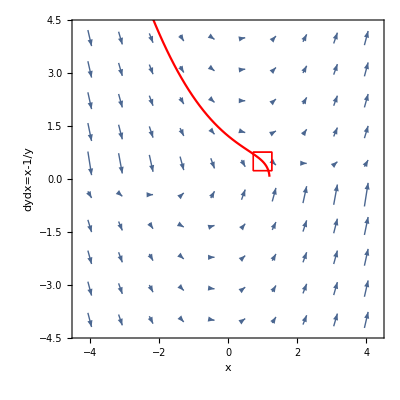

```mathematica
dfield1=VectorPlot[{1,x-1/y},{x,-4,4},{y,-4,4},Axes->True,VectorScale->{Small},VectorPoints->{10},AxesLabel->{"x","dydx=x-1/y"},GridLines->{{1},{1/2}}];
Show[dfield1, ppp1,pppl1]
```

```mathematica
Clear["Global`*"]
```

6. y' = sin^2 y, (0, -0.4), (0,1)

```mathematica
pp1=DSolve[{y'[x]==Sin[y[x]]^2,y[0]==-0.4},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},-ArcCot[2.36522+x]]}}

```mathematica
pppl1=ListPlot[{{0,-0.4}},PlotStyle->{Blue,Large},PlotMarkers->{□,19}];
```

```mathematica
pp2 = DSolve[{y'[x]==Sin[y[x]]^2,y[0]==1},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},-ArcCot[x-Cot[1]]]}}

```mathematica
pppl2=ListPlot[{{0,1}},PlotStyle->{Red,Large},PlotMarkers->{□,19}];
```

```mathematica
ppp1=Plot[y[x]/.pp1,{x,-4,4},PlotStyle->{Blue,Medium}];
ppp2=Plot[y[x]/.pp2,{x,-4,4},PlotStyle->{Red,Medium}];
```

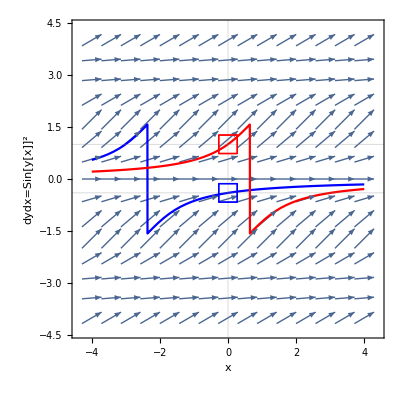

```mathematica
dfield1=VectorPlot[{1,Sin[y]^2},{x,-4,4},{y,-4,4},Axes->True,VectorScale->{Automatic},AxesLabel->{"x","dydx=Sin[y[x]]^2"},GridLines->{{0},{-0.4,1}}];
Show[dfield1, ppp1,ppp2,pppl1,pppl2]
```

```mathematica
Clear["Global`*"]
```

7. y' = ⅇ^(y/x), (2,2), (3,3)

```mathematica
pp1=NDSolve[{y'[x]==Exp[y[x]/x],y[2]==2},y,{x,-10,3.4}]
```

General::ovfl: Overflow occurred in computation.

NDSolve::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x,y[x]} = {-0.0014555,-4.78979×10^116}.

NDSolve::ndsz: At x == 3.35069, step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[{{0.0067248, 3.35069}}, <>]}}

```mathematica
pp2=NDSolve[{y'[x]==Exp[y[x]/x],y[3]==3},y,{x,-10,5}]
```

General::ovfl: Overflow occurred in computation.

NDSolve::nlnum: The function value {Overflow[]} is not a list of numbers with dimensions {1} at {x,y[x]} = {-0.00260554,-3.04976×10^97}.

{{y→InterpolatingFunction[{{0.00787501, 5.}}, <>]}}

```mathematica
ppp1 =Plot[Evaluate[y[x]/.pp1],{x,-10,3.4},PlotRange->All,PlotStyle->{Red,Medium}];
pppl1=ListPlot[{{2,2}},PlotStyle->{Red,Large},PlotMarkers->{□,19}];
ppp2 =Plot[Evaluate[y[x]/.pp2],{x,-10,5},PlotRange->All,PlotStyle->{Blue,Medium}];
```

InterpolatingFunction::dmval: Input value {-9.99973} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-9.99969} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
pppl2=ListPlot[{{3,3}},PlotStyle->{Blue,Large},PlotMarkers->{□,19}];
```

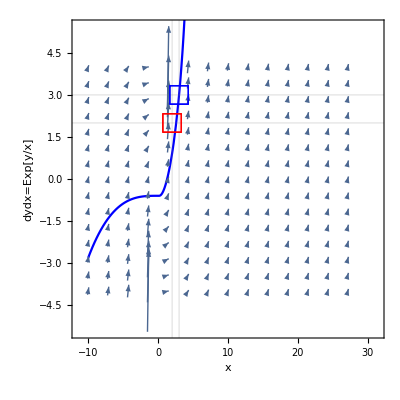

```mathematica
dfield1=VectorPlot[{1,Exp[y/x]},{x,-10,30},{y,-4,4},Axes->True,VectorScale->Automatic,AxesLabel->{"x","dydx=Exp[y/x]"},GridLines->{{2,3},{2,3}}];
Show[dfield1,ppp1,ppp2,pppl1,pppl2]
```

```mathematica
Clear["Global`*"]
```

8. y' = -2xy, (0,1/2), (0,1)

```mathematica
pp1=DSolve[{y'[x]==-2 x y[x],y[0]==1/2},y,x]
```

{{y→Function[{x},(ⅇ^(-x^2))/2]}}

```mathematica
pp2=DSolve[{y'[x]==-2 x y[x],y[0]==1},y,x]
```

{{y→Function[{x},ⅇ^(-x^2)]}}

```mathematica
ppp1=Plot[y[x]/.pp1,{x,-4,4},PlotStyle->{Blue,Medium}];
```

```mathematica
pppl1=ListPlot[{{0,1/2}},PlotStyle->{Blue,Large},PlotMarkers->{□,19}];
```

```mathematica
ppp2=Plot[y[x]/.pp2,{x,-4,4},PlotStyle->{Red,Medium}];
pppl2=ListPlot[{{0,1}},PlotStyle->{Red,Large},PlotMarkers->{□,19}];
dfield1=VectorPlot[{1,-2x y},{x,-2,6},{y,-4,4},Axes->True,VectorScale->{Automatic},AxesLabel->{"x","dydx=-2xy"},GridLines->{{0},{1/2,1}}];
```

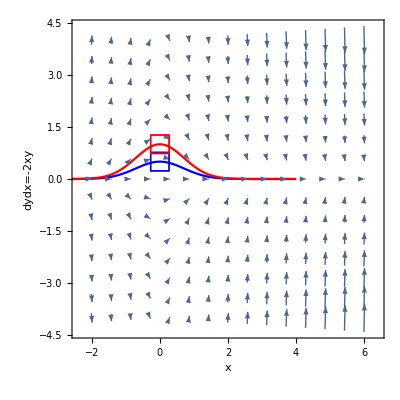

```mathematica
Show[dfield1,ppp1,ppp2,pppl1,pppl2]
```

9 - 10 Accuracy of direction fields
Direction fields are very useful because they can give you an impression of all solutions without solving the ODE, which may be difficult or even impossible. To get a feel for the accuracy of the method, graph a field, sketch solution curves in it, and compare them with the exact solutions.

9.  y' = Cos[π x]

```mathematica
Clear["Global`*"]
```

I solve the ODE, but what is wanted for the plot is the not the solution but the ODE itself.

```mathematica
sol9 =DSolve[{ y'[x]==Cos[π x]}, y, x]
```

{{y→Function[{x},C[1]+Sin[π x]/π]}}

I had to do some unexplained hand fitting of the plot, modifying the argument. It seems that StreamPlot will not conform to the domain I expected, and to show the two plots together, the function plot has to be shifted. Since the function is periodic, I assume its character is not compromised thereby.

```mathematica
pp1=Plot[Cos[π x-π/2],{x,0,2},PlotStyle->{Pink,Thickness[0.01]}];
```

I make a table to superimpose points from the customized function.

```mathematica
grek=Table[{n,Cos[π n-π/2]},{n,0,2.5,0.05}];
```

The StreamPlot is easier to manipulate than a VectorPlot, in spite of its recalcitrance. Because the first number, here 0.3, is clearly a scaling factor, I hope it is permissible to use whatever seems best for it.

```mathematica
sp1=StreamPlot[{0.3,Cos[π t]},{t,0,2},{y,-1,1}];
```

```mathematica
(*sp3=StreamPlot[{0.3,Cos[π t]},{t,0,2},{y,-1,1},Epilog->{Point[grek]}];*)
```

As far as the problem description’s call for exact solutions, I think either pp1 or lp1 can be considered an exact solution object.

```mathematica
lp1=ListPlot[grek,PlotStyle->Black];
```

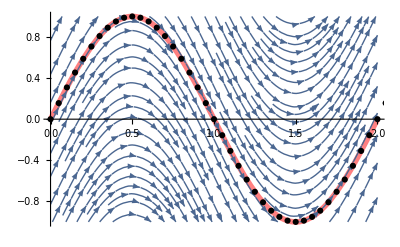

```mathematica
Show[pp1,sp3,lp1]
```

10. y' = -5y^0.5 (soln √y +5/2 x)

This problem is of interest because of the next one, 11. Problem 10 yields a solution by DSolve; however, it is impossible to check it. For problem 11 I will skip this one and do a different autonomous ODE.

```mathematica
eqn=y'[x]==-5 y[x]^0.5
```

y'[x]==-5 y[x]^0.5

```mathematica
sol=DSolve[y'[x]==-5 y[x]^0.5,y[x],x]
```

{{y[x]→0.25 (25. x^2-10. x C[1]+C[1]^2)}}

```mathematica
rdo=Simplify[eqn/.sol]
```

{y'[x]==-2.5 (25. x^2-10. x C[1]+C[1]^2)^0.5}

```mathematica
rdo1=rdo/.C[1]->1
```

{y'[x]==-2.5 (1-10. x+25. x^2)^0.5}

```mathematica
PossibleZeroQ[eqn-2.5 (1-10. x+25. x^2)^0.5]
```

False

11. Autonomous ODE. This means an ODE not showing x (the independent variable) explicitly. (The ODEs in problems 6 and 10 are autonomous.) What will the level curves f[x, y] = const (also called isoclines = curves of equal inclination) of an autonomous ODE look like?

```mathematica
Clear[y]; f[t_,y_]:=3 y;
```

The following is the plot for the autonomous ODE featured in the youtube video at https://www.youtube.com/watch?v=SB8PgHo9BIs, featuring Bill Kinney. The blue curve passes through the y-intercepts identified by their lead coefficients, and many more could be shown.

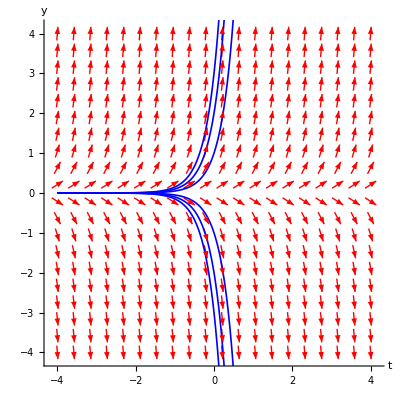

```mathematica
Show[VectorPlot[{1,f[t,y]},{t,-4,4},{y,-4,4},VectorStyle->{Thick,Red},VectorScale->{.03,.03,None},VectorPoints->20],Plot[{-2 ⅇ^(3 t),-3 ⅇ^(3t),-ⅇ^(3t),ⅇ^(3t),2 ⅇ^(3 t),3 ⅇ^(3t)},{t,-4,4},PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Blue}}],Frame->False,Axes->True,AxesLabel->{"t","y"}]
```

12 - 15 Motions
Model the motion of a body B on a straight line with velocity as given, y[t] being the distance of B from a point y = 0 at time t. Graph a direction field of the model (the ODE). In the field sketch the solution curve satisfying the given initial condition.

13. distance = velocity × time, y[1] = 1

```mathematica
fod={{0,0},{1,1},{2,2},{3,3},{4,4}}
```

{{0,0},{1,1},{2,2},{3,3},{4,4}}

The points show object B at times on x-axis, and the distance is measured vertically.

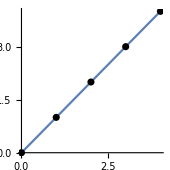

```mathematica
Plot[x,{x,0,4},ImageSize->170,AspectRatio->Automatic,Epilog->{PointSize[0.03],Point[fod]}]
```

15. Parachutist. Two forces act on a parachutist, the attraction by the earth m*g (m = mass of person plus equipment, g = 9.8 m/sec^2 the acceleration of gravity) and the air resistance, assumed to be proportional to the square of the velocity v[t]. Using Newton’s second law of motion (mass × acceleration = resultant of the forces), set up a model (an ODE for v[t]). Graph a direction field (choosing m and the constant of proportionality equal to 1). Assume that the parachute opens when v = 10 m/sec. Graph the corresponding solution in the field. What is the limiting velocity? Would the parachute still be sufficient if the air resistance were only proportional to v[t]?

There is a fully developed example at http://www.richardhitt.com/courses/354/sp00/projects/clw.pdf. It’s not done in the latest Mathematica version, but it is functional. I am taking the path of least resistance, using the text answer as a guide to the landmarks of the problem.

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=v'[t]==9.8-k/m v[t]^2/.m->80
```

v'[t]==9.8-1/80 k v[t]^2

The air resistance k is assumed to be proportional to v^2 . The text answer rolls k/m into one ball and writes

```mathematica
eqn2=v'[t]==9.8 -v[t]^2
```

v'[t]==9.8-v[t]^2

```mathematica
vout=Chop[DSolve[{eqn2,v[0]==10},v[t],t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→(3.1305 (0.523172+1. 2.71828^(6.26099 t)))/(-0.523172+2.71828^(6.26099 t))}}

Since the velocity at every integer second beyond 0 is equal to 3.13, I have to consider it to be the limiting velocity. For the limiting velocity, the text answer gives the value 3.1.

```mathematica
Table[vout/.t->n,{n,0,12}]
```

{{{v[0]→10.}},{{v[1]→3.13676}},{{v[2]→3.13051}},{{v[3]→3.1305}},{{v[4]→3.1305}},{{v[5]→3.1305}},{{v[6]→3.1305}},{{v[7]→3.1305}},{{v[8]→3.1305}},{{v[9]→3.1305}},{{v[10]→3.1305}},{{v[11]→3.1305}},{{v[12]→3.1305}}}

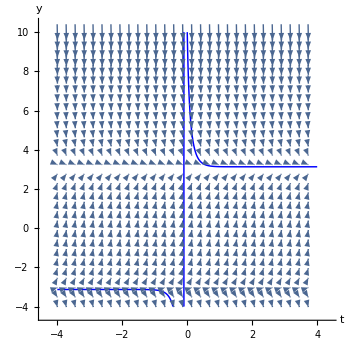

```mathematica
Show[VectorPlot[{1,9.8-y^2},{t,-4,4},{y,-4,10},VectorScale->{0.05,0.5},VectorPoints->30,ImageSize->350,Frame->False,Axes->True,AxesLabel->{"t","y"}],Plot[{(3.1304951 (0.5231+1. 2.71828^(6.26099t)))/(-0.52317+2.71828^(6.26099 t))},{t,-4,4},PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Blue}},PlotRange->{{-4,4},{-4,10}}]]
```

17 - 20 Euler’s method
This is the simplest method to explain numerically solving an ODE, more precisely, an initial value problem (IVP). (More accurate methods based on the same principle are explained in section 21.1). Using the method, to get a feel for numerics as well as for the nature of IVPs, solve the IVP numerically with a PC or calculator, 10 steps. Graph the computed values and the solution curve on the same coordinate axes.

17.  y' = y, y[0] = 1, h = 0.1

I am dodging Euler’s method. I’m not too interested in particular methods, unless they are the most efficient at a task.

```mathematica
Clear[eqn,sol]
```

```mathematica
eqn={y'[x]==y[x],y[0]==1}
```

{y'[x]==y[x],y[0]==1}

```mathematica
sol=DSolve[eqn, y[x],x]
```

{{y[x]→ⅇ^x}}

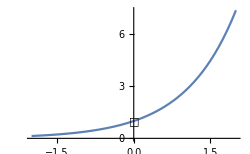

```mathematica
Plot[Exp[x],{x,-2,2},ImageSize->250,Epilog->{Text[Style[□,Large],{0.006,0.96}]}]
```

19.  y' = (y - x)^2, y[0] = 0, h = 0.1

```mathematica
Clear[eqn,sol]
```

```mathematica
eqn=y'[x]==(y[x]-x)^2
```

y'[x]==(-x+y[x])^2

```mathematica
sol=DSolve[{eqn,y[0]==0}, y[x],x]
```

{{y[x]→(1-ⅇ^(2 x)+x+ⅇ^(2 x) x)/(1+ⅇ^(2 x))}}

```mathematica
ExpToTrig[FullSimplify[sol]]
```

{{y[x]→x-Tanh[x]}}

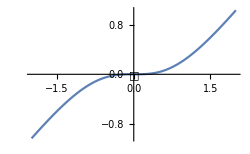

```mathematica
Plot[x-Tanh[x],{x,-2,2},ImageSize->250,Epilog->{Text[Style[□,Large],{0.01,-0.02}]}]
```